```mathematica
SetDirectory[NotebookDirectory[]];
```

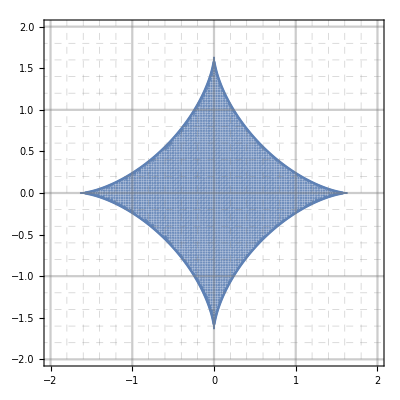

```mathematica
g=Block[{a=4/Sqrt[6],b=1/Sqrt[6],c=1/Sqrt[6],α=8/3},
Show[
RegionPlot[
(x^2+y^2-α)^3+27α x^2 y^2<0,
{x,-2,2},{y,-2,2},
PlotPoints->200
],
ParametricPlot[{
(a-b)Cos[t]+c Cos[(a-b)/b t],
(a-b)Sin[t]-c Sin[(a-b)/b t]
},{t,0,2π},
PlotStyle->Thick],
Frame->True,
LabelStyle ->{FontSize->30,FontFamily -> "Times"},
GridLines->{
Table[{i,If[IntegerQ[Rationalize[i]],Thickness[0.004],Dashed]},{i,-2,2,0.2}],
Table[{i,If[IntegerQ[Rationalize[i]],Thickness[0.004],Dashed]},{i,-2,2,0.2}]
}
]
]
```

```mathematica
Export["astroid.png",g,ImageResolution->300];
```